```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\critical_region\LPA\fixpoint_v3\nu\mub0\buffer

```mathematica
k=Flatten[Import["./k1.dat"]];
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
lam1data=Transpose[{k,lam1/k^2}];
lam2data=Transpose[{k,lam2/k}];
```

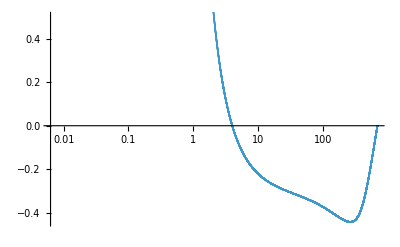

```mathematica
ListPlot[lam1data,ScalingFunctions->{"Log",Automatic}]
```

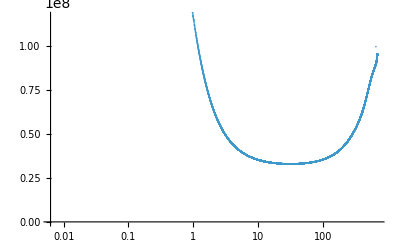

```mathematica
ListPlot[lam2data,ScalingFunctions->{"Log",Automatic}]
```